```mathematica
IntermediateFunctionLow[β_,βlow_,a_]:=a*(Max[β,βlow]-βlow)^2/β^2
IntermediateFunctionHigh[β_,b_,c_]:=b*Log[β+c]
```

```mathematica
η[x_]:=2 Log[2x]-1-2EulerGamma+(1-EulerGamma+Log[2x])/x^2
```

## σ_T

```mathematica
σTsmall[β_]:=2 β^2 (η[1/β]+1/2)
```

```mathematica
βtrans=1;
```

### Attractive

```mathematica
σTatβtrans=2.826;
```

```mathematica
σTlargeatt[β_]:=2 Log[β](Log[Log[β]]+1)
```

```mathematica
βlow=0.2;
βhigh=50;
```

```mathematica
sol=FindRoot[{σTsmall[βtrans]Exp[-(βtrans-βlow)*a]==σTatβtrans,IntermediateFunctionHigh[1,b,c]==σTatβtrans,IntermediateFunctionHigh[βhigh,b,c]==σTlargeatt[βhigh]},{{a,1},{b,4},{c,1}}]
```

{a→-0.63854,b→4.70847,c→0.822474}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β]Exp[-(Max[β,βlow]-βlow)*a]/.sol,β≤βtrans},{IntermediateFunctionHigh[β,b,c]/.sol,β>βtrans&&β<βhigh},{σTlargeatt[β],β≥βhigh}}]
```

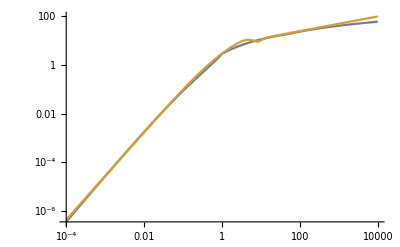

```mathematica
P1=LogLogPlot[{σT[β],(7  (β^1.8+1.4033242541563609*^-8 β^10.3))/(1+1.4 β+0.006 β^4+β^10/62500000)},{β,0.0001,10000}]
```

### Repulsive

```mathematica
σTatβtrans=1.107;
```

```mathematica
σTlargerep[β_]:=1.20*(Log[2β]-Log[Log[2β]])^2
```

```mathematica
βlow=0.2;
βhigh=50;
```

```mathematica
sol=FindRoot[{σTsmall[βtrans]Exp[-(βtrans-βlow)*a]==σTatβtrans,IntermediateFunctionHigh[βtrans,b,c]==σTatβtrans,IntermediateFunctionHigh[βhigh,b,c]==σTlargerep[βhigh]},{{a,1},{b,1},{c,1}}]
```

{a→0.532971,b→2.89927,c→0.46495}

```mathematica
σT[β_]:=Piecewise[{{σTsmall[β]Exp[-(Max[β,βlow]-βlow)*a]/.sol,β≤βtrans},{IntermediateFunctionHigh[β,b,c]/.sol,β>βtrans&&β<βhigh},{σTlargerep[β],β≥βhigh}}]
```

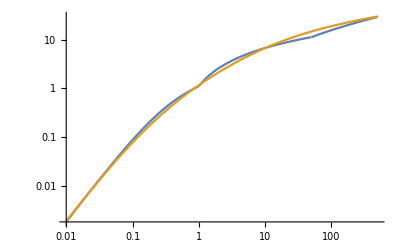

```mathematica
LogLogPlot[{σT[β],(8 β^1.8/(1+5*β^0.9+0.85*β^1.6))},{β,0.1*βlow,10*βhigh}]
```

## σ_V

```mathematica
σVsmall[β_]:=4 β^2 (η[1/(2β)]+1/2)
```

### Attractive

```mathematica
σVatβtrans=1.109;
```

```mathematica
σVlargeatt[β_]:=1/2(1+Log[β]-1/(2 Log[β]))^2
```

```mathematica
βlow=0.1;
βhigh=25;
βtrans=0.5;
```

```mathematica
sol=FindRoot[{σVsmall[βtrans]Exp[-(βtrans-βlow)*a]==σVatβtrans,IntermediateFunctionHigh[βtrans,b,c]==σVatβtrans,IntermediateFunctionHigh[βhigh,b,c]==σVlargeatt[βhigh]},{{a,0.5},{b,1},{c,1}}]
```

{a→-0.671439,b→2.53258,c→1.04944}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β]Exp[-(Max[β,βlow]-βlow)*a]/.sol,β≤βtrans},{IntermediateFunctionHigh[β,b,c]/.sol,β>βtrans&&β<βhigh},{σVlargeatt[β],β≥βhigh}}]
```

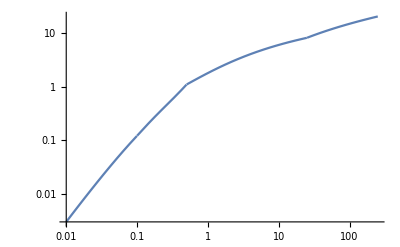

```mathematica
LogLogPlot[σV[β],{β,0.1*βlow,10*βhigh}]
```

### Repulsive

```mathematica
σVatβtrans=0.731;
```

```mathematica
σVlargerep[β_]:=Log[2β](0.793 Log[2β]-(2*0.793 -1)Log[Log[2β]])
```

```mathematica
βlow=0.1;
βhigh=25;
βtrans=0.5;
```

```mathematica
sol=sol=FindRoot[{σVsmall[βtrans]Exp[-(βtrans-βlow)*a]==σVatβtrans,IntermediateFunctionHigh[βtrans,b,c]==σVatβtrans,IntermediateFunctionHigh[βhigh,b,c]==σVlargerep[βhigh]},{{a,0.5},{b,1},{c,1}}]
```

{a→0.370562,b→2.77162,c→0.801796}

```mathematica
σV[β_]:=Piecewise[{{σVsmall[β]Exp[-(Max[β,βlow]-βlow)*a]/.sol,β≤βtrans},{IntermediateFunctionHigh[β,b,c]/.sol,β>βtrans&&β<βhigh},{σVlargerep[β],β≥βhigh}}]
```

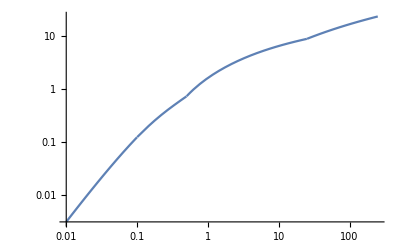

```mathematica
LogLogPlot[{σV[β]},{β,0.1*βlow,10*βhigh}]
```